1.1

1

3.1×10^14

-40 °

-0.3

-0.3

0.001

0

0

{}

-1

0.885023

1.38071

6.905

{}

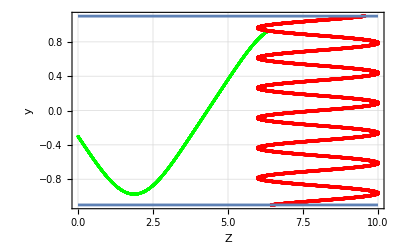

```mathematica
f[y_]:=1.4-0.18*y^4

Zf[y_]:=8+2*Sin[17.951958020513104*y]

R=1.1
n2=1
ω=3.1*10^14
α=-40 Degree
y0=-0.3

n1[y_]:=f[y]*(1-((0.35*10^14)/ω)^2)

curH=y0
step=0.001
distance=0
rayLen=0
dots=List[]
direction=-1
sinGamma=Sin[Pi/2-ArcSin[Sin[α]/n1[curH]]]
nGamma=n1[curH]


While[distance<=Zf[curH],curH+=step*Sqrt[1-sinGamma^2]*direction;
If[Abs[curH]>=R,nBeta=n2,nBeta=n1[curH]];
sinBeta=(nGamma*sinGamma)/nBeta;
If[sinBeta>1,sinBeta=sinGamma;direction*=-1];
rayLen+=step;
distance+=sinBeta*step;
sinGamma=sinBeta;
nGamma=nBeta;
AppendTo[dots,{distance,curH}];];
Print[rayLen];



rightSide={}
For[i=-R,i<R,i+=0.0001,AppendTo[rightSide,{Zf[i],i}]]

Show[ListPlot[dots,PlotStyle->{PointSize[0.005],Green},PlotRange->All,Frame->True,GridLines->Automatic,AxesLabel->{"Z","y"}],ListPlot[rightSide,PlotStyle->{PointSize[0.006],Red}, PlotRange->All,Frame->True],Plot[1.1,{x,0,10},PlotRange->{0,1.1}],Plot[-1.1,{x,0,10},PlotRange->{-1.1,0}],PlotRange->All,AxesLabel->{"Z","y"}]
```